# Efficient Mathematica Programming

## Lessons from MathGroup

Carl Woll

Wolfram Research

|     ▶

## Abstract

MathGroup frequently presents opportunities for users to develop quick, efficient code to solve a wide variety of problems. In this talk I will present various principles that I have come across in participating in these algorithmic explorations. These principles usually involve optimized data structures such as PackedArray objects and the optimal use of built-in functions, but can also include various optimizations that occur behind the scenes such as autocompilation and listability. The basic theme to all of these principles is to avoid using top-level code to do loops, and instead let the lower level internal code handle these loops.

◀     |     ▶

## Toy problem

Let's get started with the toy problem of adding 1 to a bunch of data, and a simplified discussion of functional versus procedural programming approaches. For my purposes, I'll take functional programming to mean variableless programs using pure functions and Map, while procedural programs will use variables, at the minimum including an iteration variable.

```mathematica
$HistoryLength=0;
```

### Numerical data

```mathematica
data=RandomReal[10,10^6];
```

#### Basic functional approach

```mathematica
Do[r1=#+1&/@data,{10}];//Timing
```

{1.578,Null}

#### Basic iterative approach

```mathematica
Do[r2=Table[data[[i]]+1,{i,Length[data]}],{10}];//Timing
r1===r2
```

{2.5,Null}

True

#### New version 6.0 Table syntax

```mathematica
Do[r3=Table[i+1,{i,data}],{10}];//Timing
r1===r3
```

{1.656,Null}

True

### Non-numerical data

```mathematica
data=x/@Range[10^5];
```

#### Functional

```mathematica
Do[r1=#+1&/@data,{10}];//Timing
```

{1.922,Null}

#### Procedural

```mathematica
Do[r2=Table[data[[i]]+1,{i,Length[data]}],{10}];//Timing
r1===r2
```

{2.359,Null}

True

#### Functional Table

```mathematica
Do[r3=Table[i+1,{i,data}],{10}];//Timing
r1===r3
```

{1.578,Null}

True

### Mixed numerical data

```mathematica
data=Sqrt[RandomReal[{-1,1},10^5]];
```

#### Functional

```mathematica
Do[r1=#+1&/@data,{10}];//Timing
```

{1.297,Null}

#### Procedural

```mathematica
Do[r2=Table[data[[i]]+1,{i,Length[data]}],{10}];//Timing
r1===r2
```

{1.578,Null}

True

#### Functional Table

```mathematica
Do[r3=Table[i+1,{i,data}],{10}];//Timing
r1===r3
```

{1.265,Null}

True

◀     |     ▶

### Functional programming and one-liners

Quite often on MathGroup one-liner solutions are supplied. I just want to mention that one-liner solutions are not necessarily any faster than the same solution written out using intermediate variables. Here's an example:

Richard Gaylord writes:

Given a list of numbers row={18,19,1,11,25,12,22,14}.
Select the numbers from the list by taking the largest number from the ends of the list  until the list is empty.

```mathematica
data={18,19,1,11,25,12,22,14};
```

Here is a one-liner solution proposed by Robert Hall:

```mathematica
oneliner[row_]:=Apply[(#1-#2)&,Partition[(Plus@@#)&/@NestList[If[First[#]≥Last[#],Rest[#],Drop[#,-1]]&,row,Length[row]],2,1],1]
```

It works:

```mathematica
oneliner[data]
```

{18,19,14,22,12,25,11,1}

Below I take the oneliner solution and split it up using intermediate variables:

```mathematica
nononeliner[row_]:=Module[{remainingrows, rowtotals, rowpairs},
remainingrows=NestList[If[First[#]≥Last[#],Rest[#],Drop[#,-1]]&,row,Length[row]];
rowtotals=(Plus@@#)&/@remainingrows;
rowpairs=Partition[rowtotals,2,1];
Apply[(#1-#2)&,rowpairs,1]
]
```

Now, let's compare timings for a larger example:

```mathematica
data=RandomInteger[1000,1000];
```

```mathematica
Do[r1=oneliner[data],{10}];//Timing
Do[r2=nononeliner[data],{10}];//Timing
r1===r2
```

{1.468,Null}

{1.547,Null}

True

◀     |     ▶

## Autocompilation

What happens if we use normal functions instead of pure functions? Consider:

### Pure vs ordinary (SetDelayed) functions

```mathematica
pure=#+1&;
nonpure[x_]:=x+1;
```

```mathematica
data=RandomReal[1,10^5];
```

```mathematica
Do[pure/@data,{10}];//Timing
Do[nonpure/@data,{10}];//Timing
```

{0.156,Null}

{1.344,Null}

Quite a difference. This suggests that we should try to use pure functions in our interior loops as much as possible.

### Autocompilation

What is going on here is that Mathematica' s autocompile feature is not speeding up this nonpure function. Let' s turn off autocompilation, which is a system option:

```mathematica
SystemOptions["CompileOptions"]
```

{CompileOptions→{ApplyCompileLength→∞,ArrayCompileLength→250,AutoCompileAllowCoercion→False,AutoCompileProtectValues→False,AutomaticCompile→False,CompileAllowCoercion→True,CompileConfirmInitializedVariables→True,CompiledFunctionArgumentCoercionTolerance→2.10721,CompileDynamicScoping→False,CompileEvaluateConstants→True,CompileReportCoercion→False,CompileReportExternal→False,CompileReportFailure→False,CompileValuesLast→True,FoldCompileLength→100,InternalCompileMessages→False,ListableFunctionCompileLength→250,MapCompileLength→100,NestCompileLength→100,NumericalAllowExternal→True,ProductCompileLength→250,SumCompileLength→250,SystemCompileOptimizations→All,TableCompileLength→250}}

The compile option we are interested in changing is "MapCompileLength":

```mathematica
SetSystemOptions["CompileOptions"->"MapCompileLength"->Infinity];
```

Now, let's compare them again:

```mathematica
Do[pure/@data,{10}];//Timing
Do[nonpure/@data,{10}];//Timing
```

{1.125,Null}

{1.391,Null}

Not so dramatic a difference. Let's return the system option to its original value:

```mathematica
SetSystemOptions["CompileOptions"->"MapCompileLength"->100];
```

◀     |     ▶

## Listability

As many of you probably wanted to say earlier, there are much faster ways of doing our toy problem. Basically, the fastest way to do the previous type of problem in Mathematica is to take advantage of the Listability attribute.

### Listable single argument function

Most mathematical functions are Listable, and using the Listable property is much faster than using Map and relying on autocompilation.

```mathematica
data=RandomReal[10,10^6];
```

```mathematica
r1=Sin/@data;//Timing
r2=Sin[data];//Timing
```

{0.188,Null}

{0.046,Null}

```mathematica
r1===r2
```

True

### Listable multiple argument functions

An example of a Listable multiple argument function is Plus. In this case some of the arguments can be lists and some can be scalars (not lists). For example, due to the Listable attribute of Plus, the input

```mathematica
{a,b,c}+{1,1,1}
```

gets automatically converted to

```mathematica
{a+1,b+1,c+1}
```

Similarly, the input

```mathematica
{a,b,c}+1
```

gets automatically converted to

```mathematica
{a+1,b+1,c+1}
```

Again, using Listability is much faster than using Map with autocompilation:

```mathematica
#+1&/@data;//Timing
data+1;//Timing
```

{0.156,Null}

{0.063,Null}

### Making use of Listability

#### Illustrative example

In a nutshell, Listability is an attribute which makes it possible to use vector (or in general array) operations on arrays. Consider the following matrix:

```mathematica
data=RandomInteger[{1,10},{10,2}]
```

(9 | 8
9 | 4
7 | 10
1 | 7
3 | 9
6 | 5
9 | 10
5 | 3
2 | 6
4 | 9)

Suppose we wanted to form the integer a^b from each {a,b} pair above. One possibility is to use our previous ideas here:

```mathematica
Apply[#1^#2&,data,1]
```

{43046721,6561,282475249,1,19683,7776,3486784401,125,64,262144}

However, noting that Power has the Listable attribute, we could also do:

```mathematica
data⟦All,1⟧^data⟦All,2⟧
```

{43046721,6561,282475249,1,19683,7776,3486784401,125,64,262144}

Let's compare timings with a larger data set:

```mathematica
data=RandomInteger[{1,10},{10^5,2}];
```

```mathematica
Do[r1=Apply[#1^#2&,data,1],{10}];//Timing
Do[r2=data⟦All,1⟧^data⟦All,2⟧,{10}];//Timing
r1===r2
```

{1.61,Null}

{0.328,Null}

True

#### Counting runs - Mathgroup inspired example

One common example on Mathgroup is to count the number of runs of consecutive elements there are in a list. Let's first try out the following data:

```mathematica
data=RandomInteger[1,10]
```

{0,0,1,1,1,1,0,1,1,1}

A common approach is to use Partition to create a list of pairs, and then to do some counting:

```mathematica
parts=Partition[data,2,1]
```

(0 | 0
0 | 1
1 | 1
1 | 1
1 | 1
1 | 0
0 | 1
1 | 1
1 | 1)

```mathematica
Count[parts,{1,0}]
```

3

However, given our discussion of the Listable attribute, we might try to work with the lists Most[data] and Rest[data] instead. Here we want

{0,0}->0
{0,1}->0
{1,0}->1
{1,1}->0

A Listable function that will do this is Clip[x-y,{1,1},{0,0}]:

```mathematica
Clip[{0,0,1,1}-{0,1,0,1},{1,1},{0,0}]
```

{0,0,1,0}

As an aside, there are faster Listable approaches using BitXor/BitAnd which are a bit more complex. Anyway, let's scale up this problem.

```mathematica
data=RandomInteger[1,10^6];
```

```mathematica
Do[r1=Count[Partition[data,2,1],{1,0}],{10}];//Timing
Do[r2=Tr[Clip[Most[data]-Rest[data],{1,1},{0,0}]],{10}];//Timing
r1===r2
```

{4.156,Null}

{0.563,Null}

True

◀     |     ▶

## PackedArrays

PackedArray objects were introduced in version 4, and provide memory efficient storage of arrays of numbers, and allow much more efficient implementation of many core functions of Mathematica. The only drawback to packed arrays are that the only types of numbers permitted are machine integers and real and complex machine numbers. Also, all elements in a packed array must be of the same type.

Before exploring possibilities associated with packed arrays, it is useful to first discuss the tools available to process and analyze packed arrays. Most of these tools live in the Developer` package.

### Developer`PackedArrayQ

Where possible, most Mathematica functions will return packed arrays. We can use Developer`PackedArrayQ to test this:

```mathematica
data=RandomReal[1,{100,50}];
```

```mathematica
Developer`PackedArrayQ[data]
```

True

Let's use Developer`PackedArrayQ to investigate the packed behavior of data after part assignments.

#### Simple part assignment

Simple part assignments with the right number type to packed arrays will not unpack the array:

```mathematica
data[[3,3]]=2.
```

2.

```mathematica
Developer`PackedArrayQ[data]
```

True

#### Submatrix part assignment

```mathematica
data[[{2,3},{3,4}]]=RandomReal[2,{2,2}];
Developer`PackedArrayQ[data]
```

True

```mathematica
data[[All,1]]=RandomReal[3,100];
Developer`PackedArrayQ[data]
```

True

```mathematica
data[[2;;4,3;;5]]=RandomReal[3,{3,3}];
Developer`PackedArrayQ[data]
```

True

#### Part assignments that unpack

If the right hand side is not packed, than unpacking occurs. Here is an unpacked list:

```mathematica
new={1.,2.};
Developer`PackedArrayQ[new]
```

False

We see that assigning new to data causes unpacking:

```mathematica
Developer`PackedArrayQ[data]
data[[2;;3]]=new;
Developer`PackedArrayQ[data]
```

True

False

### Developer`ToPackedArray

Developer`ToPackedArray will attempt to create a PackedArray. There will be no visible difference between the input and the output, and the only way to test if packing has occurred is to use Developer`PackedArrayQ:

#### Successful packing

```mathematica
data={1.,2.,N[Pi]}
Developer`PackedArrayQ[data]
```

{1.,2.,3.14159}

False

```mathematica
pdata=Developer`ToPackedArray[data]
Developer`PackedArrayQ[pdata]
```

{1.,2.,3.14159}

True

#### Unsuccessful packing

Here is a list that can't be packed because it contains mixed number types:

```mathematica
data={1,2.,3.}
```

{1,2.,3.}

```mathematica
pdata=Developer`ToPackedArray[data]
Developer`PackedArrayQ[pdata]
```

{1,2.,3.}

False

#### Coercion

When mixed number types are present, the optional second argument of Developer`ToPackedArray can be used to coerce the incorrect types:

```mathematica
rdata=Developer`ToPackedArray[{1.,2.,3.},Real]
Developer`PackedArrayQ[rdata]
```

{1.,2.,3.}

True

```mathematica
idata=Developer`ToPackedArray[{1.,2.,3.},Integer]
Developer`PackedArrayQ[idata]
```

{1,2,3}

True

### Developer`FromPackedArray

Developer`FromPackedArray does the obvious thing, and we'll use this function to test packed array behavior. There are situations where unpacking an array can be speed things up, but I won't be giving any such examples today

### "PackedArrayOptions"

As we saw earlier, Mathematica uses system options to control the behavior of various functions. For packed arrays, they are:

```mathematica
SystemOptions["PackedArrayOptions"]
```

{PackedArrayOptions→{ListableAutoPackLength→250,PackedArrayMathLinkRead→True,PackedArrayPatterns→True,PackedRange→True,UnpackMessage→False}}

The only option that we will use today is the last one:

```mathematica
SetSystemOptions["PackedArrayOptions"->"UnpackMessage"->True];
```

Let's try the last part assignment example again.

```mathematica
new={1.,2.,3.};
data=RandomReal[1,10];
```

```mathematica
data[[2;;4]]=new
```

Developer`FromPackedArray::unpack1: Unpacking array.

{1.,2.,3.}

These unpacking messages are useful when a packed array operation seems to be slower than expected.

◀     |     ▶

## Useful functions for packed arrays

### Part

Part assignments are quick. Here is some sample data:

```mathematica
data=RandomReal[1,{1000,1000}];
```

Create a target matrix:

```mathematica
new=ConstantArray[0,{1000,1000}];//Timing
```

{0.032,Null}

Copy data to new:

```mathematica
new[[All,All]]=data;//Timing
```

{0.14,Null}

Obviously, in this case it would be easier to just use:

```mathematica
new=data;//Timing
```

{0.,Null}

#### Mathgroup example

Yoram Pollack writes:

I am trying to create a "n x n" matrix with "1" in every position exept in
first and last row, and first and last coulumn, where "0" is needed. In
other words : sqare matrix full of  "1" sorounded by "0".

What will be the fastest and shortest way to do it?

In this case, Allan Hayes suggested to create a matrix of 1s and then to overwrite 0s in the right place.

```mathematica
f2[n_]:=Module[{tmp},
tmp=ConstantArray[1,{n,n}];
tmp[[{1,-1},All]]=0;
tmp[[All,{1,-1}]]=0;
tmp
]
```

```mathematica
f2[1000];//Timing
```

{0.031,Null}

### Clip/Unitize

Clip is a new version 5.1 function that I find very useful. The syntax is:

```mathematica
?Clip
```

RowBox[{"Clip", "[", StyleBox["x", "TI"], "]"}] gives StyleBox["x", "TI"] clipped to be between RowBox[{"-", "1"}] and RowBox[{"+", "1"}]. 
RowBox[{"Clip", "[", RowBox[{StyleBox["x", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["min", "TI"], ",", StyleBox["max", "TI"]}], "}"}]}], "]"}] gives StyleBox["x", "TI"] for RowBox[{StyleBox["min", "TI"], "≤", StyleBox["x", "TI"], "≤", StyleBox["max", "TI"]}], StyleBox["min", "TI"] for RowBox[{StyleBox["x", "TI"], "<", StyleBox["min", "TI"]}] and StyleBox["max", "TI"] for RowBox[{StyleBox["x", "TI"], ">", StyleBox["max", "TI"]}]. 
RowBox[{"Clip", "[", RowBox[{StyleBox["x", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["min", "TI"], ",", StyleBox["max", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] gives SubscriptBox[StyleBox["v", "TI"], StyleBox["min", "TI"]] for RowBox[{StyleBox["x", "TI"], "<", StyleBox["min", "TI"]}] and SubscriptBox[StyleBox["v", "TI"], StyleBox["max", "TI"]] for RowBox[{StyleBox["x", "TI"], ">", StyleBox["max", "TI"]}].

Here is a paraphrased Mathgroup example:

What is the fastest way to replace every element different from 1 by zero?

```mathematica
data=RandomInteger[10,{1000000}];
```

```mathematica
Clip[data,{1,1},{0,0}];//Timing
```

{5.58997×10^-14,Null}

```mathematica
data/.x_Integer->0/;x≠1;//Timing
```

{1.203,Null}

```mathematica
If[#===1,#,0]&/@data;//Timing
```

{1.812,Null}

Unitize[expr] is another quick function, and is basically short hand for Clip[expr, {1,1}, {0,0}].

### UnitStep

Another very quick function is UnitStep. Here is another Mathgroup example, where Larry (actuary@mchsi.com) writes:

I have two lists of real numbers, a & b.  I want to compare individual items in one list to the corresponding items in the other
list.  For example Is a[[1]] > b[[1]]. At the end of the comparisons, I want to count the "Trues".  I know how to do this use a "Table"
statement and a "Count" statement.  Is there a quicker, more efficient way of counting the number of "Trues"?

```mathematica
a=RandomReal[1,10^6];
b=RandomReal[1,10^6];
```

Using UnitStep and Total is much faster than Count:

```mathematica
r1=Count[a-b,_?Positive];//Timing
r2=Total[UnitStep[a-b]];//Timing
r1===r2
```

{1.047,Null}

{0.172,Null}

True

### BitAnd, BitXor, Total, Tr

In many of algorithms we construct an array of 0s and 1s, and BitAnd, BitXor etc are a bit faster than Plus/Times for these types of arguments. Also, Total and Tr are properly optimized for packed arrays.

### Tally

Tally is a new version 6 function that works very nicely with packed lists. For example, here is a function that does integer bin counts:

```mathematica
data=RandomInteger[100,10^6];
```

```mathematica
r1=BinCounts[data];//Timing
```

{0.734,Null}

```mathematica
r2=Tally[Range[0,100]~Join~data][[All,2]]-1;//Timing
```

{0.015,Null}

```mathematica
Rest[r1]===r2
```

True

Another nice example is an unsorted union:

```mathematica
data=RandomInteger[10^6,10^6];
```

```mathematica
r1=Union[data];//Timing
r2=Tally[data][[All,1]];//Timing
```

{0.765,Null}

{1.094,Null}

```mathematica
r1===Sort[r2]
```

True

### Ordering

Ordering is a version 4 Mathematica function which can be extremely useful. The basic situation where Ordering is useful is when one wants to sort some data, but the sort criteria isn't simple. It is possible to use Sort with a custom ordering function, but such a Sort is orders of magnitude slower than a Sort without an ordering function. Using Ordering allows one to use the default ordering function applied to a specific part of the data.

The new version 6 function SortBy can also be used for this purpose, but I find the Ordering approach to be quicker.

#### Sorting based on the last element

```mathematica
data=RandomInteger[1000,{10^5,5}];
```

```mathematica
r1=Sort[data,#1[[-1]]>#2[[-1]]&];//Timing
```

{3.609,Null}

```mathematica
r2=SortBy[data,Last];//Timing
```

{0.313,Null}

```mathematica
r3=data[[Ordering[data[[All,-1]]]]];//Timing
```

{0.047,Null}

### Transpose

With packed arrays, transposing an array is simply a matter of reindexing the packed array elements. Consequently, Transpose is a very quick operation:

```mathematica
data=RandomReal[1,{1000,1000}];
```

```mathematica
Transpose[data];//Timing
```

{0.031,Null}

#### Adding a vector to a list of points

One common operation when dealing with lists or matrices of points is to scale or translate the points. For a single point, or a list of points, the new version 6 function TransformationFunction is both powerful and quick.

```mathematica
t=TranslationTransform[{1,2}]
```

TransformationFunction[(1 | 0 | 1
0 | 1 | 2
0 | 0 | 1)]

Here is a list of a million 2-dimensional points:

```mathematica
data=RandomReal[10,{10^6,2}];
```

```mathematica
r1=t[data];//Timing
```

{0.375,Null}

As an alternative, one can use Transpose a couple times to achieve the same result:

```mathematica
r2=Transpose[Transpose[data]+{1,2}];//Timing
r1===r2
```

{0.125,Null}

True

The advantage of using TransformationFunctions is that they can handle scaling, translations and rotations, and they are not too slow.

#### Adding a vector to a matrix of points

For a matrix of points, TransformationFunction can't be used directly. For simple translations and scaling, a nested Transpose approach may be useful.

```mathematica
data=RandomReal[1,{1000,1000,2}];
```

```mathematica
r=Transpose[Transpose[data,{3,2,1}]+{1,2},{3,2,1}];//Timing
```

{0.141,Null}

```mathematica
data[[1;;3,1;;3]]
```

({0.171526,0.457742} | {0.141116,0.134321} | {0.919849,0.472374}
{0.901193,0.966108} | {0.714267,0.773909} | {0.678178,0.210094}
{0.333384,0.234867} | {0.848237,0.222702} | {0.0680551,0.485195})

```mathematica
r[[1;;3,1;;3]]
```

({1.17153,2.45774} | {1.14112,2.13432} | {1.91985,2.47237}
{1.90119,2.96611} | {1.71427,2.77391} | {1.67818,2.21009}
{1.33338,2.23487} | {1.84824,2.2227} | {1.06806,2.4852})

◀     |     ▶

## PackedArray issues

The most obvious situation where packed arrays are useful is when arithmetic is involved, since packed arrays + listability produces the fastest Mathematica code. Even with just arithmetic, though, unpacking can occur.

### Unpacking

A simple example of unpacking is division with integers. Here is a packed array of even integers:

```mathematica
data=2RandomInteger[5,10]
Developer`PackedArrayQ[data]
```

{4,2,8,2,0,2,8,8,10,2}

True

One might expect that division by 2 would be ok:

```mathematica
Developer`PackedArrayQ[data/2]
```

False

A similar example with real data:

```mathematica
data=RandomReal[{-10,10},10]
Developer`PackedArrayQ[data]
```

{-9.11831,-4.20977,9.15687,-5.71339,8.31976,-6.94131,-3.30302,0.686912,2.37831,-2.48248}

True

```mathematica
Developer`PackedArrayQ[Sqrt[data]]
```

False

In this case, coercion to complex data first may be helpful. A larger data set illustrates the advantage of avoiding unpacking here:

```mathematica
data=RandomReal[{-10,10},10^6];
cdata=Developer`ToPackedArray[data,Complex];
```

```mathematica
Sqrt[data];//Timing
Sqrt[cdata];//Timing
```

{0.797,Null}

{0.234,Null}

### Integer square roots

Suppose we are interested in finding the greatest integer less than the square root of a list of integers. How do we do this and keep everything packed?

```mathematica
data=RandomInteger[10^6,10^4];
```

```mathematica
r1=Floor[Sqrt[data]];//Timing
```

Developer`FromPackedArray::unpack: Unpacking array in call to TraditionalForm`Sqrt.

{0.844,Null}

```mathematica
r2=Floor[Sqrt[N[data]]];//Timing
```

{0.,Null}

### MathGroup example

Istvan Zachar writes:

Consider a set of data (y values):

data = Table[i*j, {i, 5}, {j, 10}]

I want to label each Integer with an x value:

label := Table[{i, #} & /@ data[[i]], {i, Length[data]}]

I've understand that list creation is much faster with Map than with Table. Is there an effective way to convert the Table to Map in the label function (either with nested Map or to incorporate the Table function into the Map)? Would it be really faster for very large datasets than with Table?

Here is a larger version of the example:

```mathematica
data=Table[i j,{i,1000},{j,1000}];
```

```mathematica
r1=Table[{i,#}&/@data[[i]],{i,Length[data]}];//Timing
```

{0.156,Null}

This speed seems fairly optimal. Some contortions are needed to convert the Table to Map, and as we've seen earlier, there isn't necessarily a large speed advantage in this conversion due to autocompilation.

#### Map version

A straightforward conversion to a Map approach is actually slower:

```mathematica
r2=Function[i,{i,#}&/@data[[i]]]/@Range[Length[data]];//Timing
r1===r2
```

{0.172,Null}

True

#### MathGroup suggestions

This post elicited several responses on MathGroup. Before testing these responses, let's turn on unpack messages.

```mathematica
SetSystemOptions["PackedArrayOptions"->"UnpackMessage"->True];
```

We will see that most of the proposed solutions did some unpacking, and were consequently not competitive in timing. A few are presented below:

```mathematica
r2=MapIndexed[First@Outer[List,#2,#1]&,data];//Timing
r1===r2
```

Developer`FromPackedArray::punpack1: Unpacking array to level TraditionalForm`1.

General::stop: Further output of TraditionalForm`Developer`FromPackedArray :: "punpack1" will be suppressed during this calculation.

{0.468,Null}

True

```mathematica
r2=MapIndexed[Thread[Append[#2,#1]]&,data];//Timing
r1===r2
```

Developer`FromPackedArray::punpack1: Unpacking array to level TraditionalForm`1.

General::stop: Further output of TraditionalForm`Developer`FromPackedArray :: "punpack1" will be suppressed during this calculation.

Developer`FromPackedArray::unpack1: Unpacking array.

General::stop: Further output of TraditionalForm`Developer`FromPackedArray :: "unpack1" will be suppressed during this calculation.

{0.531,Null}

True

```mathematica
r2=Thread/@Transpose[{Range@Length@data,data}];//Timing
r1===r2
```

Developer`FromPackedArray::punpack1: Unpacking array to level TraditionalForm`1.

General::stop: Further output of TraditionalForm`Developer`FromPackedArray :: "punpack1" will be suppressed during this calculation.

{0.422,Null}

True

#### Table + Transpose

We see that all of these suggestions were suboptimal because of unpacking. It's possible that some of the unpacking that's occuring should be eliminated, but I'll ignore that issue.

Instead, an alternative to the original poster's query is to create a table of labels, and then to use Transpose. Creating a Table, and using Transpose are safe from unpacking:

```mathematica
r2=With[{lab=Table[j,{i,1000},{j,1000}]},Transpose[{lab,data},{3,2,1}]];//Timing
r1===r2
```

{0.063,Null}

True

◀     |     ▶

## SparseArrays

Sparse arrays were introduced in version 5, and are a very useful data structure. In this talk, the only feature of SparseArrays that I want to draw your attention to are the fact that conversions between sparse arrays and normal arrays are extremely quick, as long as the size of the normal matrix isn't too large.

### Vector conversions

```mathematica
data=RandomInteger[3,10^6];
```

```mathematica
sa=SparseArray[data]//Timing
Normal[sa];//Timing
```

{0.031,SparseArray[<748900>,{1000000}]}

{0.031,Null}

### Matrix conversions

```mathematica
data=RandomInteger[3,{1000,1000}];
```

```mathematica
sa=SparseArray[data];//Timing
Normal[sa];//Timing
```

{0.032,Null}

{0.015,Null}

The down side to the speed issue is that these conversions are somewhat expensive with memory usage.

### SparseArray internal structure

The reason that the speed of conversion is of interest in this talk, is that conversion produces a SparseArray object that contains data structures that can be exploited. Here is the input form of a SparseArray object:

```mathematica
SparseArray[RandomInteger[1,10]]//InputForm
```

SparseArray[Automatic, {10}, 0, {1, {{0, 5}, {{1}, {2}, {4}, {8}, {10}}}, {1, 1, 1, 1, 1}}]

Below, I label the various pieces of the SparseArray data structure:

```mathematica
HoldForm[SparseArray][Overscript[Automatic, "not data"],Overscript[{10}, "dims"],Overscript[0, "default"],{1,{Overscript[{0,5}, Column[{"cumulative","row counts"}]],Overscript[{{2},{5},{6},{9},{10}}, "nonzero columns per row"],Overscript[{1,1,1,1,1}, "nonzero elements"]}}]//StandardForm
```

SparseArray[Automatic^(not data),{10}^dims,0^default,{1,{{0,5}^(cumulative
row counts),{{2},{5},{6},{9},{10}}^(nonzero columns per row),{1,1,1,1,1}^(nonzero elements)}}]

### SparseArray construction

By knowing the internal structure of a sparse array, it is sometimes possible to construct sparse arrays more quickly by creating the sparse array structure rather than specifying rules. For example, suppose we want to create a SparseArray object with the integers 1 to n on the superdiagonal.

```mathematica
n=10^5;
```

One method is to construct a list of rules:

```mathematica
r1=SparseArray[Table[{i,i+1}->i,{i,n-1}],{n,n}];//Timing
```

{0.578,Null}

A second method is to use a Band object:

```mathematica
r2=SparseArray[Band[{1,2}]->Range[n-1],{n,n}];//Timing
```

{0.891,Null}

The direct construction of a SparseArray data structure:

```mathematica
r3=SparseArray[Automatic,{n,n},0,{1,{Append[Range[0,n-1],n-1],List/@Range[2,n]},Range[n-1]}];//Timing
```

{0.016,Null}

```mathematica
r1===r2===r3
```

True

◀     |     ▶

## SparseArray examples

Here are a couple useful utility functions taking advantage of the quick conversion between normal and sparse vectors.

Extract the nonzero entries of a vector:

```mathematica
NonzeroEntries[data_]:=SparseArray[data]/.SparseArray[_,_,_,x_]:>x[[3]]
```

Extract the nonzero positions of a vector:

```mathematica
NonzeroPositions[data_]:=SparseArray[data]/.SparseArray[_,_,_,x_]:>Flatten[x[[2,2]]]
```

### Simple example

```mathematica
data=RandomInteger[1,10]
```

{0,0,1,0,1,0,1,0,1,0}

```mathematica
NonzeroPositions[data]
```

{3,5,7,9}

### Larger examples

```mathematica
data=RandomInteger[2,10^6];
```

Using NonzeroPositions:

```mathematica
r1=NonzeroPositions[data];//Timing
```

{0.063,Null}

Using Position:

```mathematica
r2=Position[data,Except[0],1,Heads->False];//Timing
```

Developer`FromPackedArray::unpack: Unpacking array in call to TraditionalForm`Position.

{1.047,Null}

```mathematica
r1===r2⟦All,1⟧
```

True

Alternately, one could speed up the use of Position by Unitizing and then matching with 1:

```mathematica
r3=Position[Unitize[data],1];//Timing
```

Developer`FromPackedArray::unpack: Unpacking array in call to TraditionalForm`Position.

{0.953,Null}

```mathematica
r1===r3⟦All,1⟧
```

True

### MathGroup example

Matt Pharr wrote:

I have a sparse matrix, roughly 200k by 200k, with about .01% of the
entries non zero, represented with SparseArray.  I'd like to reasonably
efficiently generate a 200k-long list where each element is the number of
non-zero entries in the corresponding row of the matrix.  I haven't been
able to figure out a quick way to do this.

Paul Abbott suggested the use of applying Differences to the right piece of the SparseArray data structure.

#### Illustrative example

```mathematica
sa=SparseArray[RandomInteger[1,{10,10}]]
```

SparseArray[<52>,{10,10}]

Paul Abbott suggested the use SparseArrayFrom the previous description, we know that we are interested in the "cumulative row counts" field of the data structure. A naive application of Part will not help here, as Part has special code to handle SparseArray objects:

```mathematica
sa[[4]]
```

Developer`FromPackedArray::unpack: Unpacking array in call to TraditionalForm`AtomQ.

SparseArray[<6>,{10}]

Here are two possibilities for extracting the cumulative row element count data:

```mathematica
rowcount=Block[{SparseArray=List},sa[[4,2,1]]]
```

{0,4,10,18,24,29,37,42,48,55,62}

```mathematica
rowcount=sa/.SparseArray[_,_,_,x_]:>x[[2,1]]
```

{0,4,10,18,24,29,37,42,48,55,62}

The row counts can now be obtained using Differences:

```mathematica
Differences[rowcount]
```

{4,6,8,6,5,8,5,6,7,7}

Since we have a matrix of 0s and 1s, we can also use Total to compare:

```mathematica
Total[sa,{2}]
```

{4,6,8,6,5,8,5,6,7,7}

#### Larger example

Here is a larger sparse array:

```mathematica
data=SparseArray[RandomInteger[2,{2000,2000}]];
```

We compare the data structure extraction procedure with Total + Clip:

```mathematica
r1=Block[{SparseArray=List},Differences[data[[4,2,1]]]];//Timing
r2=Total[Clip[data,{0,0},{1,1}],{2}];//Timing
r1===r2
```

{0.,Null}

{0.265,Null}

True

◀     |     ▶

## MathGroup: Clip + NonzeroPosition examples

Most of the examples I will present can be summarized with the following procedure. Construct some integer packed array structures representing a certain aspect of the data. Manipulate these packed arrays, making sure that they don't unpack, and produce a result.

### Extract 2D points in the third quadrant

Matt wrote:

After I posted my earlier message (the one entitled "'Good' or 'Proper' Mathematica coding habits question"), I decided to try some
timings for the last code sample I had a question on (the one trying to extract all sublists where each element of a sublist had to be negative).Here' s what I found :

Matt presented some variations on code to extract data points that were in the third quadrant.

```mathematica
L=RandomReal[NormalDistribution[0,1],{10^6,2}];
```

```mathematica
Graphics[{Point[L]},Axes->True,PlotRange->{{-6,6},{-6,6}}]
```

The most straightforward possibility is:

```mathematica
r1=Cases[L,{_?Negative,_?Negative}];//Timing
```

{3.297,Null}

Some other posted responses were:

```mathematica
Pick[L,Plus@@Sign@#&/@L,-2];//Timing
Pick[L,Total@Transpose@Sign@L,-2];//Timing
```

{1.813,Null}

{1.563,Null}

We can do this much  more quickly by applying Sign, then adding the pairs, finally clipping to -2.

```mathematica
Style[Row[{L[[;;10]],"   ⟹^Sign   ",Sign[L[[;;10]]],"   ⟹^Total   ",List/@Total[Sign[L[[;;10]]],{2}],"   ⟹^Clip   ",Clip[List/@Total[Sign[L[[;;10]]],{2}],{-2,-2},{0,0}]}],ScriptSizeMultipliers->1]
```

(-2.23002 | 6.4696
-1.66893 | 3.75318
-5.6178 | 4.82439
-2.04943 | 8.75825
7.75889 | -9.97856
4.29349 | 2.88849
-3.76451 | 5.61683
-6.18678 | -1.44152
-0.563675 | -7.06283
3.79417 | 2.61382)   ⟹^Sign   (-1 | 1
-1 | 1
-1 | 1
-1 | 1
1 | -1
1 | 1
-1 | 1
-1 | -1
-1 | -1
1 | 1)   ⟹^Total   (0
0
0
0
0
2
0
-2
-2
2)   ⟹^Clip   (0
0
0
0
0
0
0
-2
-2
0)

```mathematica
r2=Module[{tmp},
tmp=Sign[L];
tmp=Total[tmp,{2}];
tmp=Clip[tmp,{-2,-2},{0,0}];
tmp=NonzeroPositions[tmp];
L[[tmp]]
];//Timing
```

{0.141,Null}

```mathematica
r1===r2
```

True

Let's check that r2 is indeed all in the third quadrant:

```mathematica
Graphics[Point[r2],Axes->True,PlotRange->{{-6,6},{-6,6}}]
```

### SplitAt

Robert Brambilla writes:

I have a list (very long, thousands, and unsorted) of numbers r = {n1, n2 ...}
  and for a given a number m I want to split it in the two sublists
  (unsorted, same order) u = {elements < m], v = {elements > m}.

Probably the simplest approach is to use Select (or Cases):

```mathematica
data=RandomReal[10,10^6];
```

```mathematica
r1={Cases[data,x_/;x<3],Cases[data,x_/;x≥3]};//Timing
```

{4.531,Null}

Now, a much faster approach will rely on UnitStep to convert data to 0s and 1s, and then NonzeroPositions to extract the 1s (or 0s) as appropriate:

```mathematica
Style[Row[{List/@data[[;;10]],"   ⟹^(subtract  3)   ",List/@data[[;;10]]-3,"   ⟹^UnitStep   ",List/@UnitStep[data[[;;10]]-3],"   ⟹^NonzeroPositions   "}],ScriptSizeMultipliers->1]
```

(8.93843
5.68054
0.733493
5.74377
9.33132
5.42338
9.07063
2.73698
9.21772
6.07967)   ⟹^(subtract  3)   (5.93843
2.68054
-2.26651
2.74377
6.33132
2.42338
6.07063
-0.263025
6.21772
3.07967)   ⟹^UnitStep   (1
1
0
1
1
1
1
0
1
1)   ⟹^NonzeroPositions

```mathematica
r2=With[{d=UnitStep[data-3]},
{data[[NonzeroPositions[BitXor[1,d]]]],data[[NonzeroPositions[d]]]}];//Timing
```

{0.234,Null}

```mathematica
r1===r2
```

True

◀     |     ▶

## MathGroup: Part examples

### Faster version of Complement

A MathGroup poster wanted a version of Complement that was faster than Complement:

in the list:
pp=Table[Random[Integer, {1, 1000}], {i, 1000}];
how could i know which numbers from 1 to 1000 does not exist in the pp List, but without using:
Complement[Table[i,{i,1000}],pp]

In this case, we want the integers between 1 and 10^6 that are missing from data.

```mathematica
data=RandomInteger[{1,10^6},10^6];
```

```mathematica
r1=Complement[Range[10^6],data];//Timing
```

{1.407,Null}

Since Complement sorts its result (and so its worst case complexity is O(n log n)), we should be able to come up with a nonsorting O(n) algorithm that beats Complement. Here is an example:

```mathematica
Style[Row[{List/@Range[10],"   ⟹^Part   ",tmp=Range[Length[data]];tmp[[data]]=0;List/@tmp[[;;10]],"   ⟹^NonzeroEntries"}],ScriptSizeMultipliers->1]
```

(1
2
3
4
5
6
7
8
9
10)   ⟹^Part   (0
0
0
4
0
0
7
8
9
10)   ⟹^NonzeroEntries

```mathematica
r2=Module[{all=Range[Length[data]]},
all[[data]]=0;
NonzeroEntries[all]
];//Timing
```

{0.219,Null}

```mathematica
r1===r2
```

True

### Inverse permutation

Diana wrote

[snip]

I want to figure out a clean way to code its inverse permutation.

One idea is to use Ordering:

```mathematica
data=Ordering[RandomReal[1,10^6]];
```

```mathematica
r1=Ordering[data];//Timing
```

{0.719,Null}

Another idea is to use Part:

```mathematica
r2=Module[{tmp=data},tmp[[tmp]]=Range[Length[tmp]];tmp];//Timing
```

{0.141,Null}

```mathematica
r1===r2
```

True

◀     |     ▶

## MathGroup: Accumulate example

### Markov sequence

Yaroslav Butatov asks:

I'm looking for a fast way to sample from a Markov-1 sequence of
random bits. The method below is 3600 times slower than built-in
RandomInteger function, can it be made much faster?

p = 0.9; (* the probability of encountering 00 or 11 *)
f = RandomChoice[{p^# (1 - p)^(1 - #), p^(1 - #) (1 - p)^#} -> {1, 0}]&;
NestList[f, RandomChoice[{0, 1}], 100000]

Here we can think of the Markov-1 sequence as being generated by a list of boolean toggles that indicate whether the next element of the sequence should change or remain the same:

```mathematica
Grid[{Riffle[{0,0,1,0,1,1,0,0,0,1,1},StringReplace["  ⟹^#  ","#":>ToString[#]]&/@{False,True,True,True,False,True,False,False,True,False}]
},Spacings->.1]
```

0 |   ⟹^False   | 0 |   ⟹^True   | 1 |   ⟹^True   | 0 |   ⟹^True   | 1 |   ⟹^False   | 1 |   ⟹^True   | 0 |   ⟹^False   | 0 |   ⟹^False   | 0 |   ⟹^True   | 1 |   ⟹^False   | 1

This problem doesn't at first appear to be amenable to Listable operations, since we need to repeatedly apply a custom function to an
initial value. However, there is at least one kernel function, Accumulate, that very quickly applys a particular function (Plus) to an
initial value.

If we use 0 to represent False and 1 to represent True, then we can generate the above sequence by prepending an initial value to the boolean list and using Accumulate:

```mathematica
Grid[{Riffle[{0,0,1,0,1,1,0,0,0,1,1},StringReplace["  ⟹^#  ","#":>"+"<>ToString[#]]&/@Boole[{False,True,True,True,False,True,False,False,True,False}]],
Table["",{10}]~Join~{Style["↓",30],"  Accumulate"}~Join~Table[SpanFromLeft,{9}],
Riffle[{0,0,1,2,3,3,4,4,4,5,5},"  ⟹  "],
Table["",{10}]~Join~{Style["↓",30],"  modulo 2"}~Join~Table[SpanFromLeft,{9}],
Riffle[Mod[{0,0,1,2,3,3,4,4,4,5,5},2],"  ⟹  "]
},Alignment->{Left,{Baseline,Center,Baseline,Center,Baseline}},Spacings->{0.1,1}]
```

0 |   ⟹^(+0)   | 0 |   ⟹^(+1)   | 1 |   ⟹^(+1)   | 0 |   ⟹^(+1)   | 1 |   ⟹^(+0)   | 1 |   ⟹^(+1)   | 0 |   ⟹^(+0)   | 0 |   ⟹^(+0)   | 0 |   ⟹^(+1)   | 1 |   ⟹^(+0)   | 1
 |  |  |  |  |  |  |  |  |  | ↓ |   Accumulate |  |  |  |  |  |  |  |  | 
0 |   ⟹   | 0 |   ⟹   | 1 |   ⟹   | 2 |   ⟹   | 3 |   ⟹   | 3 |   ⟹   | 4 |   ⟹   | 4 |   ⟹   | 4 |   ⟹   | 5 |   ⟹   | 5
 |  |  |  |  |  |  |  |  |  | ↓ |   modulo 2 |  |  |  |  |  |  |  |  | 
0 |   ⟹   | 0 |   ⟹   | 1 |   ⟹   | 0 |   ⟹   | 1 |   ⟹   | 1 |   ⟹   | 0 |   ⟹   | 0 |   ⟹   | 0 |   ⟹   | 1 |   ⟹   | 1

To generate a list where toggles occur 10% of the time, we can use the following:

```mathematica
toggles=UnitStep[RandomInteger[{-9,0},10^6]];//Timing
```

{0.031,Null}

Then, the code to generate the Markov sequence is:

```mathematica
r=BitAnd[Accumulate[Prepend[toggles,0]],1];//Timing
```

{0.031,Null}

This can be compared with:

```mathematica
RandomInteger[1,10^6];//Timing
```

{0.016,Null}

◀     |     ▶

## MathGroup: Total examples

### Count identical submatrices

Yaroslav Bulatov wrote:

What is the recommended way of counting the number of matches in two
lists?

The natural way would be to thread over Equal, but Equal will evaluate
before Thread gets to it. The method below works, but somehow feels
wrong

m1 = RandomInteger[{1}, {10^5, 2, 2}];
m2 = RandomInteger[{1}, {10^5, 2, 2}];
matches = Thread[temporary[m1, m2]] /. temporary -> Equal;
Count[matches, True]

```mathematica
m1=RandomInteger[{1},{10^5,2,2}];
m2=RandomInteger[{1},{10^5,2,2}];
```

Here is Yaroslav's solution:

```mathematica
Count[Thread[temporary[m1,m2]]/.temporary->Equal,True]//Timing
```

{0.359,6306}

We can do this much  more quickly by applying subtracting, using Unitize and adding up the elements of each matrix. Then, use Total and Unitize again producing a 0 for identical submatrices.

```mathematica
Row[{Column[MatrixForm/@m1[[;;5]],ItemSize->{4,3}]-Column[MatrixForm/@m2[[;;5]],ItemSize->{4,3}],"   ⟹^subtract   ",Column[MatrixForm/@(m1-m2)[[;;5]],ItemSize->{4,3}],"   ⟹^Unitize   ",Column[MatrixForm/@Unitize[(m1-m2)[[;;5]]],ItemSize->{4,3}],"   ⟹^Total   ",Column[Total[Unitize[(m1-m2)[[;;5]]],{2,3}],ItemSize->{4,3},Alignment->Center],"   ⟹^Unitize   ",Column[Unitize[Total[Unitize[(m1-m2)[[;;5]]],{2,3}]],ItemSize->{4,3},Alignment->Center],"   ⟹^Total"}]
```

(1 | 0
0 | 1)
(0 | 0
1 | 1)
(0 | 1
1 | 1)
(0 | 1
0 | 0)
(1 | 1
1 | 0)-(1 | 0
0 | 1)
(0 | 0
1 | 0)
(0 | 1
1 | 0)
(1 | 1
0 | 1)
(0 | 1
1 | 1)   ⟹^subtract   (0 | 0
0 | 0)
(0 | 0
0 | 1)
(0 | 0
0 | 1)
(-1 | 0
0 | -1)
(1 | 0
0 | -1)   ⟹^Unitize   (0 | 0
0 | 0)
(0 | 0
0 | 1)
(0 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)   ⟹^Total   0
1
1
2
2   ⟹^Unitize   0
1
1
1
1   ⟹^Total

Here is the code that does this:

```mathematica
Length[m1]-Total[Unitize[Total[Unitize[m1-m2],{2,3}]]]//Timing
```

{0.047,6306}

### Repeated Dot

Gregory Lypny wrote:

x and y are both 2000 x 3 matrices.  I wanted to created a 2000 x 1  
vector with each element equal to the dot product of the  
corresponding rows of x and y.  So I tried this:

Table[x[[i]].y[[i]], {i, 1, 2000}]

It took more than two and a half minutes on my iBook G4.  Is that  
normal?  I've done seemingly more demanding computations in Do loops  
and Tables that are completed in a split second.  Am I doing  
something wrong with this one?

It turns out that Gregory was not using packed arrays for x and y (a result of using division with integer packed arrays). However, using the Listable paradigm, we can just use Times + Total to improve speed.

```mathematica
x=RandomReal[1,{1000000,3}];
y=RandomReal[1,{1000000,3}];
```

```mathematica
r1=Table[Dot[x[[i]],y[[i]]],{i,1000000}];//Timing
r2=Total[x y,{2}];//Timing
r1==r2
```

{0.89,Null}

{0.25,Null}

True

◀     |     ▶

## NearestFunction

The new version 6 function Nearest creates a NearestFunction data structure that very quickly returns the nearest element of the data to a given point. The key thing to remember with Nearest is that the creation of the NearestFunction can be time consuming, but once created, applying the NearestFunction to data is extremely quick.

### Naive application of Nearest

```mathematica
data=RandomReal[10,10^6];
```

A naive application of Nearest:

```mathematica
Nearest[data,6]//Timing
```

{0.688,{6.}}

This seems rather slow, and it is when compared to a straightfoward Listable approach as described earlier:

```mathematica
data[[Ordering[Abs[data-6],1]]]//Timing
```

{0.078,{6.}}

### Intended application of Nearest

Of course, the above is not the proper way to appreciate Nearest and NearestFunction. Instead, use Nearest to create a NearestFunction:

```mathematica
(nf=Nearest[data])//Timing
```

{0.656,NearestFunction[{1000000,1},<>]}

Now, apply this NearestFunction to data:

```mathematica
nf[6]//Timing
```

{0.016,{6.}}

The application of NearestFunction to data is quick.

#### Comparison of NearestFunction and Ordering approaches

Consider a secondary data source:

```mathematica
data2=RandomReal[10,10^2];
```

Here we calculate the points in data nearest to data2 using both methods:

```mathematica
r1=data[[Ordering[Abs[data-#],1]]]&/@data2;//Timing
```

{6.844,Null}

```mathematica
r2=nf/@data2;//Timing
```

{2.781,Null}

So, the NearestFunction is faster. However, it turns out there is currently an inefficiency in NearestFunction when it is mapped over data, and using Table instead of Map is considerably quicker:

```mathematica
r3=Table[nf[i],{i,data2}];//Timing
```

{0.719,Null}

#### Comparison of NearestFunction and Ordering approaches to k-nearest neighbors

It turns out that Ordering[data,1] is considerably quicker than Ordering[data,2], and so using NearestFunction to find multiple nearest neighbors is even better:

```mathematica
r1=data[[Ordering[Abs[data-6],2]]]//Timing
r2=nf[6,2]//Timing
```

{0.75,{6.,6.00001}}

{0.031,{6.,6.00001}}

## NearestFunction example

Here is a recent example inspired by a Mathgroup post by Gareth Russell:

What is the fastest way to compute the nearest point to point distance between two data sets?

This is a very nice example for using NearestFunction. First, create some data:

```mathematica
data1=RandomReal[NormalDistribution[0,.5],{100000,2}];
data2=RandomReal[NormalDistribution[3,.1],{100000,2}];
```

```mathematica
plot=Graphics[{GraphicsComplex[Join[data1,data2],{Blue,Point[Range[Length[data1]]],Green,Point[Range[Length[data1]+1,Length[data1]+Length[data2]]]}]},Axes->True]
```

Apply Nearest to the first data set to obtain a NearestFunction:

```mathematica
(nf=Nearest[data1])//Timing
```

{0.188,NearestFunction[{100000,2},<>]}

Apply the NearestFunction to the second data set:

```mathematica
g=Table[nf[i],{i,data2}]⟦All,1⟧;//Timing
```

{2.625,Null}

For each member of the second list, we now have the corresponding member of the second list that is closest, so we need to evaluate these distances and choose the smallest:

```mathematica
(closest=Ordering[Sqrt[Total[(g-data2)^2,{2}]],1])//Timing
```

```mathematica
Show[plot,Graphics[{Red,PointSize[Large],Point[g⟦closest⟧],Point[data2⟦closest⟧]}]]
```

◀     |     ▶

## InterpolatingFunction

Interpolation with InterpolationOrder->0 is a nice technique to convert numerical data in a piecewise manner. Interpolation constructs an InterpolatingFunction object, and this construction can be time consuming. However, the application of this InterpolatingFunction object to data is very quick because InterpolatingFunction objects due a binary search to pick out the right piece of the interpolation.

### MathGroup example

Jacob Rome wrote:

I have a seemingly simple problem. I want to find the element in a
list that is closest to a number I specify. In my case, I have a list
of about 30,000 numbers (y[i]). I want to find the closest match for
each of about 10,000 other numbers (call them x[i]). Obviously, speed
is important. I've sorted the large list, and right now I'm going
through each y[i] from lowest to highest and testing it to see if x[i]
is less than that value. This takes about .1 seconds for each x[i].

I'm wondering if anyone has had a similar problem, and if there is a
better function built-in to Mathematica. Alternatetively, I could
build my own. I've just recently realized that I could also reduce the
search time considerably if I sort the x[i] list as well, and only
start my search from where I last left off.  Any ideas on which
approach would be more efficient? Thanks.

This is a good problem for NearestFunction, but if we are only interested in the closest data point, we can boost speed by using an InterpolatingFunction instead.

```mathematica
makeinterp[y_]:=Module[{sy},
sy=Sort[y];
Interpolation[
Transpose[{ListCorrelate[{1/2,1/2},sy,1,Last@sy],sy}],
InterpolationOrder->0
]
]
```

#### Illustrative example

```mathematica
data={0,1,2,4,7,10,11,13};
```

```mathematica
if=makeinterp[data];
```

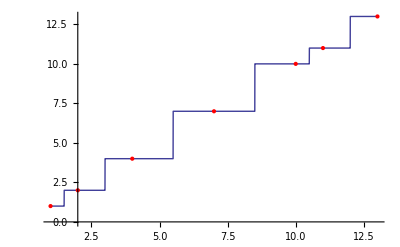

```mathematica
Show[Plot[if[x],{x,1,13}],Graphics[{Red,PointSize[Large],Point[Transpose[{data,data}]]}]]
```

#### Large example

```mathematica
data=Sort@RandomReal[10,10^5];
```

```mathematica
Timing[nf=Nearest[data]]
Timing[if=makeinterp[data]]
```

{1.1241×10^-15,NearestFunction[{100000,1},<>]}

{0.531,InterpolatingFunction[(0.000055198 | 9.99993),<>]}

A secondary data source:

```mathematica
data2=RandomReal[{.01,9.99},10^4];
```

And some timings:

```mathematica
r1=Table[nf[i],{i,data2}];//Timing
r2=if/@data2;//Timing
```

{3.844,Null}

{0.078,Null}

```mathematica
Max[Abs[r1-r2]]
```

0.

◀     |     ▶

## Conclusion

In conclusion, my primary message is to try to incorporate PackedArrays into your solutions, and use the tools I've presented to make sure that unpacking doesn't occur. And of course, try to learn what system and internal functions are available to use as tools.

When this talk is uploaded to the library, I will include the URLs of all of the quoted MathGroup threads.

◀     |